## Figure 2C, 2D

Evaluate notebook to generate plots for Fig. 2C (surviving species),  and 2D (effective number of species).

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarLogPlots`"];
```

### get colorscheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

### import and process data

```mathematica
path="data\\";
```

```mathematica
params=Import[path<>"lDiversity_s1pt4_epsilonSet.mx"];
epsilon=Table[params[[i,1]]^2/params[[i,2]],{i,9}];
numConditions=Length[epsilon];
```

```mathematica
allStrats=Import[path<>"lDiversity_s1pt4_strats.mx"];
allFP=Import[path<>"lDiversity_s1pt4_allFP.mx"];
```

```mathematica
lengths=Length/@allFP;
```

```mathematica
validFPIndices=Position[lengths,x_/;x==10];
```

```mathematica
(*delete cases that failed*)
```

```mathematica
validFP=allFP[[validFPIndices//Flatten]];
validFP=validFP[[1;;400]];
```

```mathematica
validStrats=allStrats[[validFPIndices//Flatten]];
```

### effective species

```mathematica
effectiveSpecies[n_]:=
Module[{},
relN=n/Total[n];
modN=relN/.{x_/;x<0->0};
entropyTable=Table[-modN[[i]]*Log[modN[[i]]],{i,Length[modN]}]//Quiet;
entropyTable2=entropyTable/.{Indeterminate->0};
entropy=entropyTable2//Total;
mEff=E^entropy
]
```

```mathematica
effectiveSpecies=Table[effectiveSpecies[validFP[[i,j]]],{i,Length[validFP]},{j,Length[params]}];
```

```mathematica
transposedSpecies=effectiveSpecies//Transpose;
```

```mathematica
meanEffSpeciesChanges=Mean/@transposedSpecies;
stdEffSpeciesChanges=StandardDeviation/@transposedSpecies;
```

```mathematica
effOrderedPairs=Transpose[{epsilon,meanEffSpeciesChanges}];
effOorderedPairsError=Table[{effOrderedPairs[[i]],ErrorBar[stdEffSpeciesChanges[[i]]]},{i,Length[params]}];
```

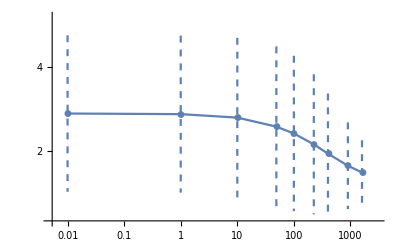

```mathematica
ErrorListLogLinearPlot[effOorderedPairsError,TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.01,.1,1,10,100,1000,10000},Range[0,6,1]},PlotRange->{{5*10^-3,3000},{.3,5.2}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic,ErrorBarFunction->(ErrorBarPlots`Private`ebarfun[##]/.l_Line:>{Dashed,l}&)]
```

```mathematica
Export["fig2D_effectiveNumberSpecies.svg",%];
```

### species richness

```mathematica
getRichness[n_]:=Block[{},
nTotal=Total[n];
cutoff=10^-6;
richness=Count[n,x_/;x>cutoff]
]
```

```mathematica
m=10;
```

```mathematica
richnessTable=Table[getRichness[validFP[[i,j]]]/m,{i,Length[validFP]},{j,Length[params]+1}];
```

```mathematica
transposedRichness=richnessTable//Transpose;
```

```mathematica
meanRichness=Mean/@transposedRichness;
stdRichness=StandardDeviation/@transposedRichness;
```

```mathematica
richnessOrderedPairs=Transpose[{Join[epsilon,{0}],meanRichness}];
richnessOrderedPairsError=Table[{richnessOrderedPairs[[i]],ErrorBar[stdRichness[[i]]]},{i,Length[params]+1}];
```

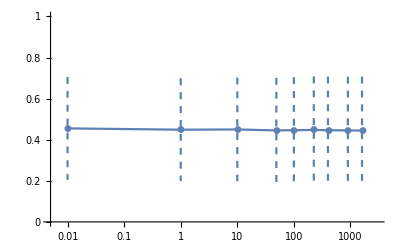

```mathematica
ErrorListLogLinearPlot[richnessOrderedPairsError[[1;;-2]],TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.01,.1,1,10,100,1000,10000},Transpose[{Range[0,1,.2],{"0","0.2","0.4","0.6","0.8","1"}}]},PlotRange->{{5*10^-3,3000},{0,1}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic,ErrorBarFunction->(ErrorBarPlots`Private`ebarfun[##]/.l_Line:>{Dashed,l}&),AxesOrigin->{5*10^-3,0}]
```

```mathematica
Export["fig2C_speciesRichness.svg",%];
```